```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[ρ, B][x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}]//FullSimplify;
Subscript[ns, F][x_]=2*Subscript[ρ, F][x,x];
Subscript[ns, C][x_]=(ⅇ^(-2 x^2) (-2 x-ⅇ^(x^2) √π (1+2 x^2) Erf[x]))/π;
```

#### Real Space Density Profile

Here we calculate the real space density profile for two spinors with mixed wave function at t = 0

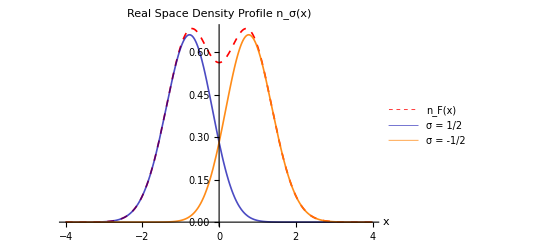

```mathematica
p1=Plot[{Subscript[ns, F][x],0.5*(Subscript[ns, F][x] + Subscript[ns, C][x]),0.5*(Subscript[ns, F][x] - Subscript[ns, C][x])},{x,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Real Space Density Profile n_σ(x)",Bold,16],PlotLegends->{"n_F(x)","σ = 1/2","σ = -1/2"},AxesLabel->{"x"}]
```

#### Momentum Space Density Profile

Here we plot the momentum space density profile for t = 0

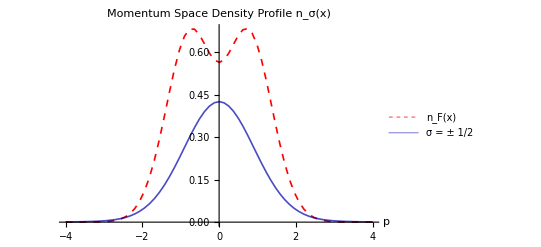

```mathematica
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
Subscript[n, B][p_] :=Subscript[n, B][p]= 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
p2=Plot[{Subscript[n, F][p],0.25*(Subscript[n, F][p] + Subscript[n, B][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_σ(x)",Bold,16],PlotLegends->{"n_F(x)","σ = ± 1/2"},AxesLabel->{"p"},PlotPoints->5,MaxRecursion->4]
```

#### Momentum Space Density Profile - Dynamical Fermionization

Here we plot the momentum space density profile after the trapping potential has been turned off and t → ∞

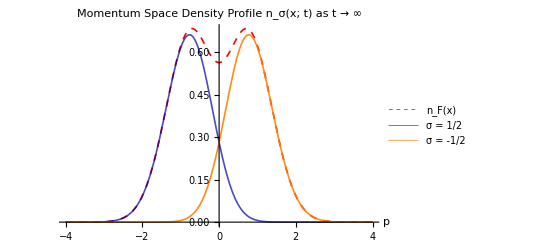

```mathematica
Subscript[n, C][p_]=(ⅇ^(-2 p^2) (-2 p-ⅇ^(p^2) √π (1+2 p^2) Erf[p]))/π;
p3=Plot[{Subscript[n, F][p],0.5*(Subscript[n, F][p] + Subscript[n, C][p]),0.5*(Subscript[n, F][p] - Subscript[n, C][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_σ(x; t) as t → ∞",Bold,16],PlotLegends->{"n_F(x)","σ = 1/2","σ = -1/2"},AxesLabel->{"p"}]
```